### Categorization

Workflow

Wolfram/PacletCICD

Wolfram`PacletCICD`

Wolfram/PacletCICD/ref/CreateALicenseEntitlementID

Synonyms

### Keywords

Details

Create a License Entitlement ID for GitHub Actions

Configure your GitHub repository with a Wolfram Engine license key so that it can launch Wolfram kernels in workflows.

Create a license entitlement

Create an on-demand license entitlement using CreateLicenseEntitlement:

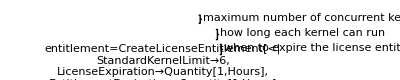

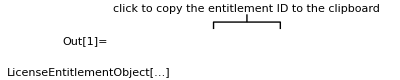

Click the entitlement ID in the output to copy it to the clipboard.

Add the license entitlement to a GitHub repository

Visit your GitHub repository in a web browser and open the settings page:

-Graphics-

Under the “Security” section, navigate to the “Actions” page under “Secrets” using the menu on the left and then click the “New repository secret” button at the top-right:

-Graphics-

Enter “WOLFRAMSCRIPT_ENTITLEMENTID” for the name and paste in the value you copied from the first step as shown below:

-Graphics-

Click the “Add secret” button.

Create a workflow

Create a workflow for your repository using CreateWorkflow:

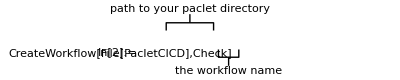

File[H:\Documents\PacletCICD\.github\workflows\CheckPaclet.yml]

Commit the workflow to your repository

Commit and push the changes to your GitHub repository.

The workflow should now start running automatically whenever you push changes to the default branch.

## See Also

Related Functions

Related Guides

## Tech Notes

## Related Links